## Division de l’octave en 12 parties égales :

```mathematica
Table[2^(k/12),{k,0,12}]//N
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775,2.}

```mathematica
Solve[{td^7 tc^5==2,4tc==5td},{tc,td}][[4]]
```

{tc→5^(7/12)/(2 2^(1/12)),td→2^(11/12)/5^(5/12)}

```mathematica
{5^(7/12)/(2 2^(1/12)),2^(11/12)/5^(5/12)}//N
```

{1.20675,0.965399}

```mathematica
tc/td/.{tc->5^(7/12)/(2 2^(1/12)),td->2^(11/12)/5^(5/12)}
```

5/4

```mathematica
5./53
```

0.0943396

```mathematica
{1,tc,tc td,tc^2 td,tc^2 td^2 ,tc^2 td^3,tc^3 td^3,tc^3 td^4,tc^4 td^4,tc^4 td^5,tc^5 td^5,tc^5 td^6,tc^5 td^7}/.{tc->5^(7/12)/(2 2^(1/12)),td->2^(11/12)/5^(5/12)}//N
```

{1.,1.20675,1.16499,1.40585,1.35721,1.31025,1.58114,1.52643,1.84202,1.77828,2.14594,2.07168,2.}

## Schéma des quintes ascendantes :

```mathematica
Table[(3/2)^k,{k,0,11}]//N
```

{1.,1.5,2.25,3.375,5.0625,7.59375,11.3906,17.0859,25.6289,38.4434,57.665,86.4976}

## Quintes ascendantes ramenées à une octave unique :

```mathematica
Table[2^(k/12),{k,0,12}]//N
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775,2.}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]
```

{1,3/2,9/8,27/16,81/64,243/128,729/512,2187/2048,6561/4096,19683/16384,59049/32768,177147/131072}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]
```

{1,2187/2048,9/8,19683/16384,81/64,177147/131072,729/512,3/2,6561/4096,27/16,59049/32768,243/128}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]]
```

{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}

```mathematica
1200Log[2,#]&/@Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]]//N
```

{113.685,90.225,113.685,90.225,113.685,90.225,90.225,113.685,90.225,113.685,90.225}

```mathematica
1200Log[2,#]&/@Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]]//N
```

{23.46,90.225,90.225,113.685,90.225,113.685,90.225,90.225,113.685,90.225,113.685,90.225}

```mathematica
Total[{23.460010384649014,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305}]
```

1109.78

```mathematica
Log[2,#]&/@{3,4,5}
```

{Log[3]/Log[2],2,Log[5]/Log[2]}

```mathematica
Apply[Times,{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}]
```

243/128

```mathematica
2^7
```

128

```mathematica
(3/2.)^12
```

129.746

```mathematica
{2187/2048.,256/243.}
```

{1.06787,1.0535}

```mathematica
2187/2048/(256/243)//N
```

1.01364

```mathematica
{1200Log[2,2187/2048],1200Log[2,256/243]}//N
```

{113.685,90.225}

```mathematica
113.68500605771193/90.22499567306305
```

1.26002

## Schéma des quintes descendantes :

```mathematica
Table[(3/2)^k,{k,0,-11,-1}]//N
```

{1.,0.666667,0.444444,0.296296,0.197531,0.131687,0.0877915,0.0585277,0.0390184,0.0260123,0.0173415,0.011561}

## Quintes descendantes ramenées à une octave unique :

```mathematica
Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]
```

{256/243,65536/59049,32/27,8192/6561,4/3,1024/729,262144/177147,128/81,32768/19683,16/9,4096/2187,2}

```mathematica
Ratios[Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]]
```

{256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,2187/2048}

```mathematica
NestWhile[#/2&,15,#≥2&]
```

15/8

```mathematica
7/6//N
```

1.16667

```mathematica
7/5//N
```

1.4

```mathematica
7/4//N
```

1.75

```mathematica
8/7//N
```

1.14286

```mathematica
8/5//N
```

1.6

```mathematica
9/8//N
```

1.125

```mathematica
Rationalize[N[Table[2^(k/12),{k,12}]],0.02]
```

{17/16,9/8,6/5,5/4,4/3,7/5,3/2,8/5,5/3,9/5,15/8,2}

```mathematica
Rationalize[N[Table[2^(k/19),{k,19}]],0.02]
```

{27/26,14/13,9/8,7/6,6/5,5/4,9/7,4/3,7/5,10/7,3/2,14/9,8/5,5/3,12/7,9/5,13/7,21/11,2}

```mathematica
Rationalize[N[Table[2^(k/11),{k,18}]],0.02]
```

{16/15,8/7,6/5,9/7,11/8,13/9,11/7,5/3,7/4,15/8,2,15/7,9/4,12/5,18/7,11/4,29/10,28/9}

```mathematica
(2187 256)/(2048 243)
```

9/8

```mathematica
1200. Log[2,9/8]
```

203.91

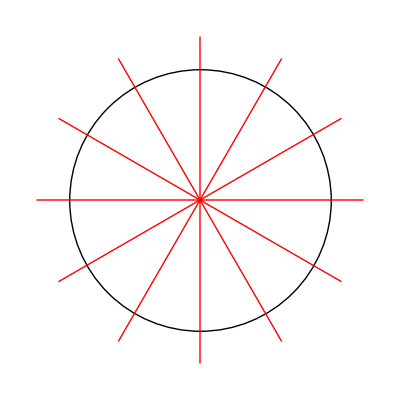

```mathematica
Graphics[{Circle[{0,0},2],Red,Table[Line[{{0,0},{2.5Cos[(2k π)/12],2.5Sin[(2k π)/12]}}],{k,0,11}]}]
```

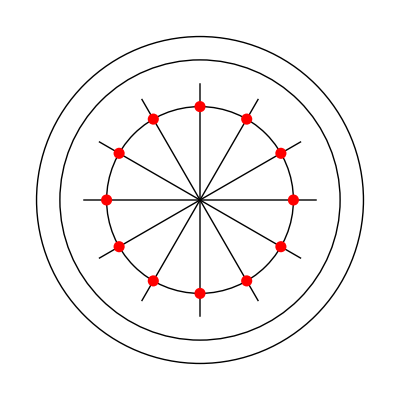

```mathematica
Graphics[{Circle[{0,0},2],Circle[{0,0},3],Circle[{0,0},3.5],Table[Line[{{0,0},{2.5Cos[(2k π)/12],2.5Sin[(2k π)/12]}}],{k,0,11}],Red,PointSize[0.02],Table[Point[{2Cos[(2k π)/12],2Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
tc=1200  Log[2,2187/2048];td=1200 Log[2,256/243];
```

```mathematica
{tc,td,tc+ td,tc- td}//N
```

{113.685,90.225,203.91,23.46}

```mathematica
intervencents={0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td};
```

```mathematica
Accumulate[intervencents]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78,1200.}

```mathematica
notesdebase=Most[Accumulate[intervencents]]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78}

```mathematica
1109.78-203.91
```

905.87

```mathematica
touteslesnotes=Sort[Join[notesdebase,Mod[notesdebase+tc,1200.],Mod[notesdebase-tc,1200.]]]
```

{0.,23.46,90.225,113.685,203.91,294.135,317.595,384.36,407.82,498.045,521.505,588.27,611.73,701.955,792.18,815.64,905.865,996.09,1019.55,1086.31,1109.78}

```mathematica
Append[Differences[touteslesnotes],90.22499567306306]
```

{23.46,66.765,23.46,90.225,90.225,23.46,66.765,23.46,90.225,23.46,66.765,23.46,90.225,90.225,23.46,90.225,90.225,23.46,66.765,23.46,90.225}

```mathematica
8 (113.685)+4 66.765
```

1176.54

```mathematica
2.td-tc
```

66.765

```mathematica
td
```

(1200 Log[256/243])/Log[2]

```mathematica
2^((2td-tc)/1200)//Simplify
```

134217728/129140163

```mathematica
Total[%]
```

Total::normal: Nonatomic expression expected at position 1 in Total[134217728/129140163].

Total[134217728/129140163]

```mathematica
Length[touteslesnotes]
```

21

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

```mathematica
Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,0,21}]
```

{Point[{3 Cos[Mod[1/600 (300-List) π,2 π]],3 Sin[Mod[1/600 (300-List) π,2 π]]}],Point[{1.83697×10^-16,3.}],Point[{0.367583,2.9774}],Point[{1.36512,2.67141}],Point[{1.68216,2.48402}],Point[{2.62824,1.4465}],Point[{2.99859,0.0921128}],Point[{2.98728,-0.275991}],Point[{2.71207,-1.28245}],Point[{2.5345,-1.60509}],Point[{1.52652,-2.58259}],Point[{1.19858,-2.75017}],Point[{0.184139,-2.99434}],Point[{-0.184139,-2.99434}],Point[{-1.52652,-2.58259}],Point[{-2.5345,-1.60509}],Point[{-2.71207,-1.28245}],Point[{-2.99859,0.0921128}],Point[{-2.62824,1.4465}],Point[{-2.4312,1.75763}],Point[{-1.68216,2.48402}],Point[{-1.36512,2.67141}]}

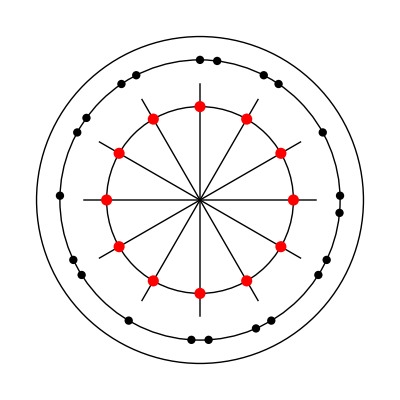

```mathematica
Graphics[{Circle[{0,0},2],Circle[{0,0},3],Circle[{0,0},3.5],PointSize[0.015],Table[Line[{{0,0},{2.5Cos[(2k π)/12],2.5Sin[(2k π)/12]}}],{k,0,11}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.02],Table[Point[{2Cos[(2k π)/12],2Sin[(2k π)/12]}],{k,0,11}]}]
```

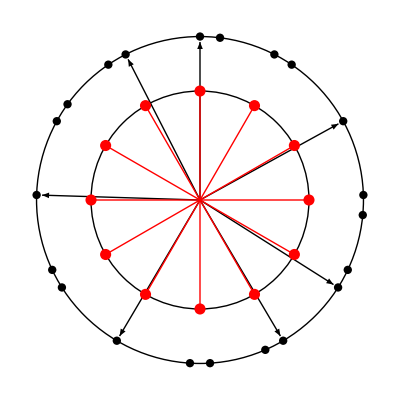

```mathematica
Graphics[{Circle[{0,0},2],Circle[{0,0},3],PointSize[0.015],Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,Table[Line[{{0,0},{2Cos[(2k π)/12],2Sin[(2k π)/12]}}],{k,0,11}],PointSize[0.02],Table[Point[{2Cos[(2k π)/12],2Sin[(2k π)/12]}],{k,0,11}]}]
```

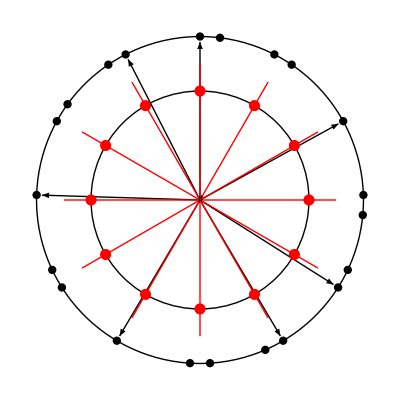

```mathematica
Graphics[{Text["ABCDEF",{0.5,0.5}],Circle[]}]
```

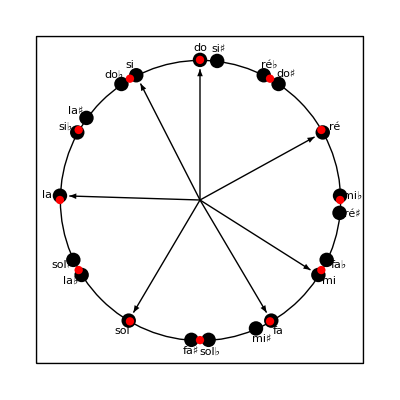

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[notes21[[k]],{3.28Cos[theta[touteslesnotes[[k]]]],3.25Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

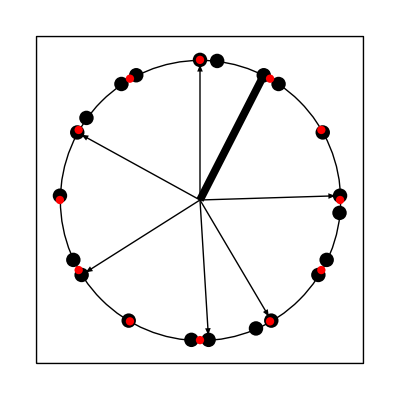

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[3]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[3]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

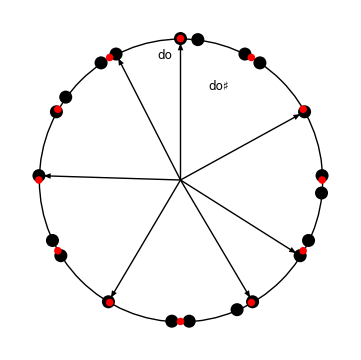

```mathematica
s[q_]:=Mod[300-600 q/π,1200]
```

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

```mathematica
s[theta[1.1]]
```

1.1

```mathematica
theta[905.87]
```

3.11086

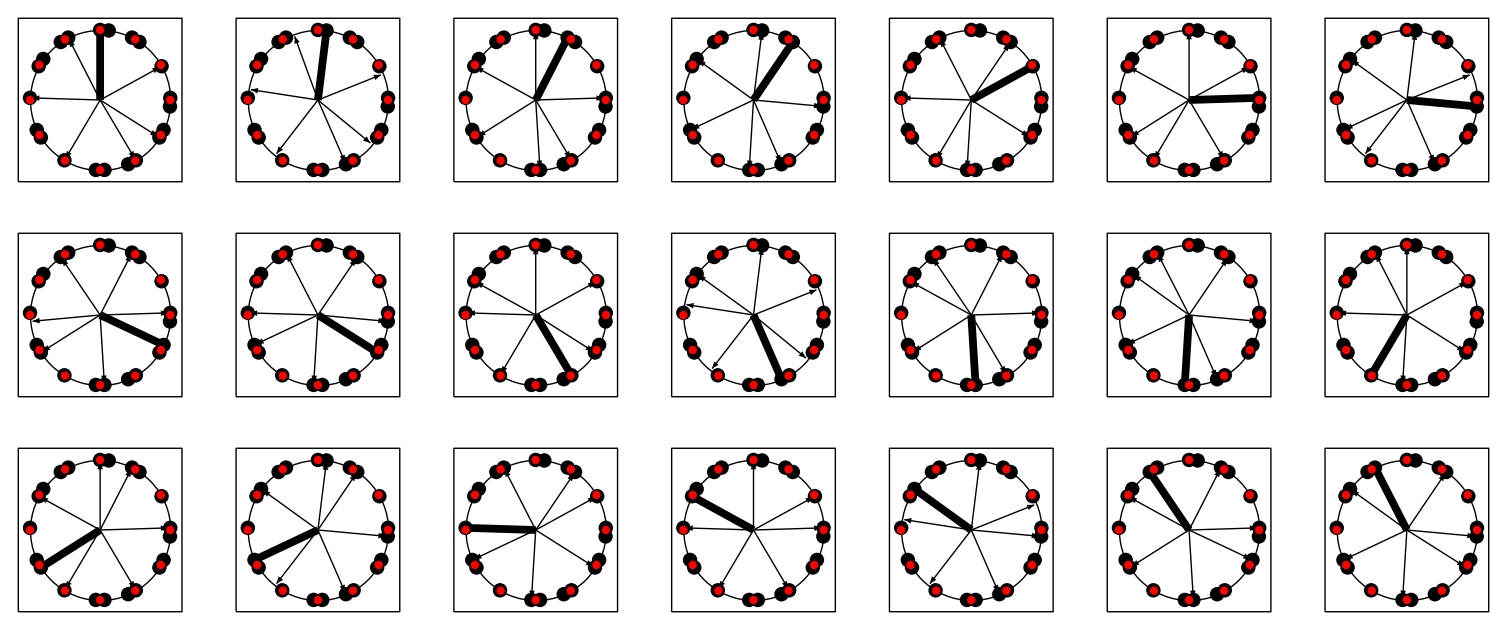

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[k]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[k]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{k,21}],7]]
```

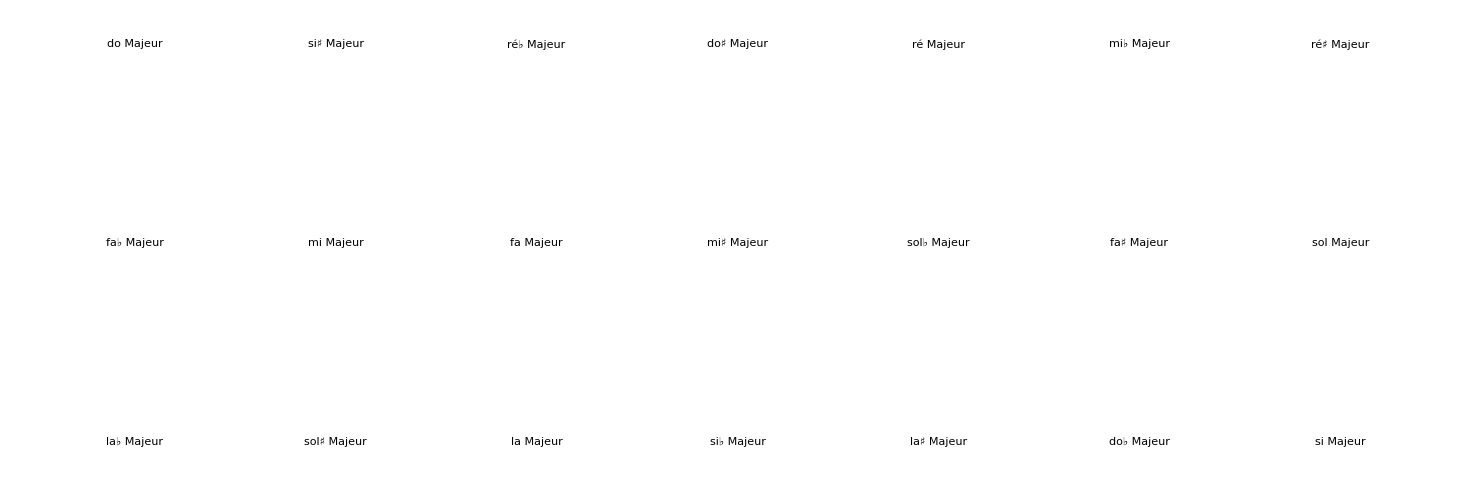

```mathematica
GraphicsGrid[Partition[Table[Labeled[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[k]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[k]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],modesmajeurs[[k]]],{k,21}],7]]
```

```mathematica
modesmajeurs={"do Majeur","si♯ Majeur","ré♭ Majeur","do♯ Majeur","ré Majeur","mi♭ Majeur","ré♯ Majeur","fa♭ Majeur","mi Majeur","fa Majeur","mi♯ Majeur","sol♭ Majeur","fa♯ Majeur","sol Majeur","la♭ Majeur","sol♯ Majeur","la Majeur","si♭ Majeur","la♯ Majeur","do♭ Majeur","si Majeur"}
```

{do Majeur,si♯ Majeur,ré♭ Majeur,do♯ Majeur,ré Majeur,mi♭ Majeur,ré♯ Majeur,fa♭ Majeur,mi Majeur,fa Majeur,mi♯ Majeur,sol♭ Majeur,fa♯ Majeur,sol Majeur,la♭ Majeur,sol♯ Majeur,la Majeur,si♭ Majeur,la♯ Majeur,do♭ Majeur,si Majeur}

```mathematica
notes21={"do","si♯","ré♭","do♯","ré","mi♭","ré♯","fa♭","mi","fa","mi♯","sol♭","fa♯","sol","la♭","sol♯","la","si♭","la♯","do♭","si"}
```

{do,si♯,ré♭,do♯,ré,mi♭,ré♯,fa♭,mi,fa,mi♯,sol♭,fa♯,sol,la♭,sol♯,la,si♭,la♯,do♭,si}